# Physics 230 -- Lab 10 (Linear Algebra)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics and Astronomy, Fall 2011

In most fields of science and engineering, the easiest multi-variable problems are the "linear" ones, where the unknown quantities appear in linear combinations with constant coefficients.  Linear problems are usually solved by straightforward methods and have exact solutions.  Non-linear problems, on the other hand, can become arbitrarily difficult very quickly.  In this lab, we will explore matrix and vector properties and operations, practice formulating problems in terms of matrix/vector equations, and learn how to use Mathematica's linear-algebra capabilities to solve simple and moderately-challenging math and physics problems.

If you haven’t taken linear algera yet, don’t worry.  We’ll use Mathematica introduction the concepts you’ll need to know at this point.  After you take linear algebra, you may want to revisit Mathematica and this notebook to see the richness of its possibilities here.

```mathematica
Clear["`*"]
```

## Matrix and vector algebra (65 min)

### (#1) Matrix multiplication (15 min)

Mathematica's matrix multiplication operation is called Dot ("."), the same operator used for vector muliplication.  This makes sense because they are mathematically the same thing.  Names for this operation include "dot" product, "scalar" product, "inner product" and "vector product." The dot product of two vectors is a term-by-term multiplication of corresponding elements and then taking the sum of those products.  For instance, the dot product of (a, b, c) and (d, e, f) is ad+be+cf.  Doing this in Mathematica,

```mathematica
v1={a,b,c};
v2={d,e,f};
MatrixForm/@{v1,v2}
v3=v1.v2
```

{(a
b
c),(d
e
f)}

a d+b e+c f

There is a subtle point to notice about MatrixForm.  It is useful for displaying vectors and matrices in easily readable form, but they need to be in InputForm for the operations to work.

With matrix multiplication each element in the product is the dot product of the corresponding row in the first matrix and the corresponding column in the second matrix.  Let’s consider a 2×2 matrix first because its simpler.  Let A=(a | b
c | d) and B=(e | f
g | h).  Then the (2,1) element of the product of A and B would be the dot product of the second row of A and the first column of B, ce+dg.  The entire product would be

```mathematica
A={{a,b},{c,d}};
B={{e,f},{g,h}};
MatrixForm/@{A,B,A.B}
```

{(a | b
c | d),(e | f
g | h),(a e+b g | a f+b h
c e+d g | c f+d h)}

a) Two matrices are not required to have the same number of dimensions in order to multiply them together.  However, the number of columns in the first matrix must equal the number of rows in the second matrix.  If, for example, A is and m×n matrix and B is a n×p matrix, then A.B will be an m×p matrix.  Evaluate the examples below to see this.

```mathematica
A= {{1,2,3},{4,5,6},{7,8,9}};
B= {{9,8,7},{6,5,4},{3,2,1}};
MatrixForm/@{A,B,A.B}
MatrixForm/@{B,A,B.A}
```

{(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),(9 | 8 | 7
6 | 5 | 4
3 | 2 | 1),(30 | 24 | 18
84 | 69 | 54
138 | 114 | 90)}

{(9 | 8 | 7
6 | 5 | 4
3 | 2 | 1),(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),(90 | 114 | 138
54 | 69 | 84
18 | 24 | 30)}

```mathematica
A= {{1,2},{3,4},{5,6}};
B = {{8,7,6,5},{4,3,2,1}};
MatrixForm/@{A,B,A.B}
MatrixForm/@{B,A,B.A}
```

{(1 | 2
3 | 4
5 | 6),(8 | 7 | 6 | 5
4 | 3 | 2 | 1),(16 | 13 | 10 | 7
40 | 33 | 26 | 19
64 | 53 | 42 | 31)}

Dot::dotsh: Tensors {{8, 7, 6, 5}, {4, 3, 2, 1}} and {{1, 2}, {3, 4}, {5, 6}} have incompatible shapes.

{(8 | 7 | 6 | 5
4 | 3 | 2 | 1),(1 | 2
3 | 4
5 | 6),{{8,7,6,5},{4,3,2,1}}.{{1,2},{3,4},{5,6}}}

(b) Evaluate these examples, which contain vectors that are constructed with dimension = 2.

```mathematica
A = {{1},{2},{3}};
B = {{3,2,1}};
MatrixForm/@{A,B,A.B}
```

{(1
2
3),(3 | 2 | 1),(3 | 2 | 1
6 | 4 | 2
9 | 6 | 3)}

```mathematica
A = {{1,2,3}};
B = {{3},{2},{1}};
MatrixForm/@{A,B,A.B}
```

{(1 | 2 | 3),(3
2
1),(10)}

(c) When vectors are treated normally as objects of dimension = 1, they automatically behave as expected whether appearing on the left or on the right of the Dot operator.  MatrixForm might fool you into thinking otherwise, since it always displays them as column vectors.  But the intrinsic behavior of Dot is very straightforward (a_1 b_1+a_2 b_2 + ...) and handles things in the expected way.

```mathematica
A = {1,2,3};
B = {3,2,1};
MatrixForm/@{A,B,A.B}
```

{(1
2
3),(3
2
1),10}

```mathematica
A= {{1,2,3},{4,5,6},{7,8,9}};
B = {3,2,1};
MatrixForm/@{A,B,A.B}
MatrixForm/@{B,A,B.A}
```

{(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),(3
2
1),(10
28
46)}

{(3
2
1),(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),(18
24
30)}

### (#2) Algebraic properties of matrix multiplication (5 min)

(a) Evaluate the cell below to define four 2×2 matrices (a, b, c and e).

```mathematica
a = {{a11,a12},{a21,a22}}; b = {{b11,b12},{b21,b22}}; c = {{c11,c12},{c21,c22}}; e = {{1,0},{0,1}};
```

(b) Compute  a.e – a to show that e is an identity matrix under matrix multiplication.

```mathematica
a.e-a
a.e
```

{{0,0},{0,0}}

{{a11,a12},{a21,a22}}

(c) Compute  a.(b.c)  and  (a.b).c to show that matrix multiplication is associative.  Use MatrixForm to display your results.  You might need to Simplify.

```mathematica
a.(b.c)//Simplify//MatrixForm
(a.b).c//Simplify//MatrixForm
```

(a11 b11 c11+a12 b21 c11+a11 b12 c21+a12 b22 c21 | a11 b11 c12+a12 b21 c12+a11 b12 c22+a12 b22 c22
a21 b11 c11+a22 b21 c11+a21 b12 c21+a22 b22 c21 | a21 b11 c12+a22 b21 c12+a21 b12 c22+a22 b22 c22)

(a11 b11 c11+a12 b21 c11+a11 b12 c21+a12 b22 c21 | a11 b11 c12+a12 b21 c12+a11 b12 c22+a12 b22 c22
a21 b11 c11+a22 b21 c11+a21 b12 c21+a22 b22 c21 | a21 b11 c12+a22 b21 c12+a21 b12 c22+a22 b22 c22)

(d) Compute  a.b  and  b.a to show that matrix multiplication is not commutative.  Some matrices commute, but most don't!  Use MatrixForm to display your results.  You might need to Simplify.

```mathematica
a.b//Simplify//MatrixForm
b.a//Simplify//MatrixForm
```

(a11 b11+a12 b21 | a11 b12+a12 b22
a21 b11+a22 b21 | a21 b12+a22 b22)

(a11 b11+a21 b12 | a12 b11+a22 b12
a11 b21+a21 b22 | a12 b21+a22 b22)

(e) Compute a.a^-1 using Inverse and show that it is equal to the identity matrix e.  Use MatrixForm to display your results.  You might need to Simplify.

```mathematica
a.Inverse[a]//Simplify//MatrixForm
```

(1 | 0
0 | 1)

### (#3) Determinant and Trace (10 min)

(a) Use Diagonal to extract the diagonal elements from the matrix M below, and then Apply the Plus operation to obtain the sum of the diagonal elements.

```mathematica
M = {{1,2,3},{3,1,2},{2,3,1}};  M//MatrixForm
Plus@@Diagonal[M]
```

(1 | 2 | 3
3 | 1 | 2
2 | 3 | 1)

3

(b) Now use Tr to calculate the trace of matrix M.  Don't be surprised if you get the same result as in the previous step.  A matrix's trace is defined as the sum of its diagonal elements.

```mathematica
Tr[M]
```

3

(c) Use Det to compute the determinant of M.  The determinant of a matrix is equal to the volume of the parallelepiped whose edges are the three column vectors (or row vectors) of the matrix.

```mathematica
Det[M]
```

18

(e) Use Inverse to compute M^-1 and then calculate its determinant.  How are the determinants of M and M^-1related?

```mathematica
Det[Inverse[M]]
```

1/18

### (#4) Rotation matrices (5 min)

(a) When a matrix operates (via standard "dot" product multiplication) on a vector, the vector is transformed into a different vector.  The graphic below shows how the matrix (cos(θ) | -sin(θ)
sin(θ) | cos(θ)) rotates a the pink vector counter-clockwise by the angle θ.  Alternatively, we can adopt the "coordinate transformation" view by saying that the vector itself remains stationary while the entire coordinate system is rotated in the opposite direction (clockwise).  Click on the graphic to see the coordinate transformation.  In the first picture, the vector {1,0} is moved to a new location, {cos(θ),sin(θ)}.  In the second picture, the vector {1,0} does not move, but is equivalently described as {cos(θ), sin(θ)} in the rotated x'y' coordinate system.  Think about this and explain both pictures to your TA.

```mathematica
lab[txt_,loc_] := Text[Style[txt,FontSize->18],1.07*loc];
label1 = {lab["θ",{0.25,0.1}],Arrow[{{0.45,0.05},{0.35,0.30}}],Blue,lab["x",{Sqrt[2],0}],lab["y",{0,Sqrt[2]}]};
label2 = {lab["θ",{0.25,-0.1}],Arrow[{{0.45,-0.05},{0.35,-0.30}}],Red,lab["y'",{1,1}],lab["x'",{1,-1}]};

coord1= {Arrowheads[0.05],Blue,Arrow[Sqrt[2]{{-1,0},{1,0}}],Arrow[Sqrt[2]{{0,-1},{0,1}}]};
coord2= {Arrowheads[0.05],Red,Dashed,Arrow[{{-1,-1},{1,1}}],Arrow[{{-1,1},{1,-1}}]};

vec1 = {Arrowheads[0.1],Pink,Thickness[0.015],Arrow[{{0,0},{1,1}/Sqrt[2]}]};
vec2 = {Arrowheads[0.1],Pink,Thickness[0.015],Arrow[{{0,0},{1,0}}]};

pica = Graphics[{coord1,label1,vec1},AspectRatio->Automatic,AxesLabel->{"x","y"}];
picb = Graphics[{coord1,coord2,label2,vec2},AspectRatio->Automatic,AxesLabel->{"x","y"}];

FlipView[{pica,picb}]
```

Rotation matrices are part of a general class of matrices which perform operations on a vector without changing its length.  These matrix have the property that the absolute value of their determinant is the identity matrix.  (More generally that the matrix times its Hermitian adjoint is one.)

(b)  Construct the rotation matrix  S = (1/(√2) | -1/(√2)
1/(√2) | 1/(√2)), and describe the its rotation angle (magnitude and direction) to your TA.  Hint: Try operating on the vector v = {1,0}.

```mathematica
{1,0}.({{1/(√2), -1/(√2)}, {1/(√2), 1/(√2)}})//MatrixForm
```

(1/(√2)
-1/(√2))

### (#5) Linear coordinate transformations (5 min)

2D matrices can produce a variety of different linear transformations, including rotations, reflections, inversions, expansion/compressions, shears, or any combination of these factors.  "Linear" just means that when a matrix operates on a vector, the new vector components are all linear combinations of the old components.  That's exactly what matrix multiplication does!  In contrast, a non-linear transformation might square one of the vector components or multiply a few components together or worse.  We like linear problems because they usually have exact answers that can be obtained in a straightforward way.

In the cell below, we construct several transformation matrices and graphically illustrate each linear transformation.  Evaluate the cell and explain why each matrix does what it does.

```mathematica
objects = {{EdgeForm[Thick],FaceForm[None],Rectangle[]},{AbsolutePointSize[10],Point[{0,0}],Red,Point[{1,0}],Blue,Point[{0,1}],Pink,Point[{1,1}]}};
seeit[mat_]:=Graphics[GeometricTransformation[objects,mat],Axes->True,AspectRatio->Automatic,Frame->True,PlotRange->3{{-1,1},{-1,1}},PlotLabel->mat]

identity = {{1,0},{0,1}};
rotate45 = {{1,-1},{1,1}}/Sqrt[2];
rotate90 = {{0,-1},{1,0}};
stretchy = {{1,0},{0,2}};
compressx = {{1/2,0},{0,1}};
shearx = {{1,1},{0,1}};
reflectx ={{-1,0},{0,1}};
invert = {{-1,0},{0,-1}};

matrixlist = {identity,rotate45,rotate90,stretchy,compressx,shearx,reflectx,invert};
seeit/@ matrixlist
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### (#6) Similarity transforms (5 min)

(a) In addition to transforming vectors, matrix multiplication can also be used to transform other matrices into a new coordinate systems.  In this example, we create a matrix S that rotates the coordinate system by 120° around the {1,1,1} direction, effectively permuting the x, y and z axes, i.e. z → x, x → y, y → z.  We also create a matrix M_1 that produces a 180° rotation around the z axis.  The resulting transformations are illustrated here via their effects on vector  v = {1, 2, 3}.  Make sure that you understand the output.

```mathematica
vec = {1,2,3};

S = {{0,0,1},{1,0,0},{0,1,0}};(* 120° rotation around {1,1,1} direction -- permutes x,y,z axes *)
MatrixForm/@ {S,vec,S.vec} 

M1 = {{-1,0,0},{0,-1,0},{0,0,1}};(* 180° rotation around the z axis *)
MatrixForm/@ {M1,vec, M1.vec}
```

{(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0),(1
2
3),(3
1
2)}

{(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1),(1
2
3),(-1
-2
3)}

(b) To transform matrix M_1 into the permuted coordinate system associated with S, we just matrix multiply with S on the left and S^-1on the right, i.e. M_2 = S.M_1.S^-1.  This is called a "similarity" transform, and requires that S be invertible.  If two matrices are related by a similarity transform, we say that they are "similar."  In some sense, similar matrices are really the same matrix operation displayed in two different coordinate systems.  Construct the matrix M_2 and observe its effect on vector v = {1,2,3}.  Explain the behavior of M_2 to your TA in terms of its similarity to M_1.

```mathematica
M2= S.M1.Inverse[S];
MatrixForm/@{M2,vec,M2.vec}
```

{(1 | 0 | 0
0 | -1 | 0
0 | 0 | -1),(1
2
3),(1
-2
-3)}

### (#7) Diagonalization (10 min)

In the cell below, compute the matrix that contains the three Eigenvectors of a, Transpose it, and call the result c.  Then compute d = c^-1·a·c.  How do the diagonal elements of d compare to the Eigenvalues of a?

```mathematica
Clear["`*"]
```

```mathematica
a = {{1,2,3},{2,1,2},{3,2,1}};
c =Transpose[Eigenvectors[a]];
d = Inverse[c].a.c;
Diagonal[d]//Simplify
Eigenvalues[a]
```

{1/2 (5+√41),-2,1/2 (5-√41)}

{1/2 (5+√41),-2,1/2 (5-√41)}

It should be clear by now that d and a are "similar" matrices.  This means that, in some sense, a and d represent the same matrix operation, but are displayed in two different coordinate systems.  Thus, the eigenvectors of a are the basis vectors of a new coordinate system in which matrix  a appears in diagonal form.  To say that a matrix is "diagonalizable" is to say that it similar to a diagonal matrix, or to say that its matrix of eigenvectors is invertible, or that its eigenvalues are linearly independent.

The eigenvalues and eigenvectors of a matrix have important physical applications.  Some of these will be illustrated in the sections below.  An example from classical mechanics the rotation of a rigid body.  An example from electricity and magnetism is the index of refraction.  An example from quantum mechanics involves stationary states of a system.

In your introductory classical mechanics class, you learned that torque τ on a body is related to its angular acceleration α by the moment of intertia I.  You may have only considered these three quantities as scalars, but torque and angular acceleration are actually vectors.  That means the moment of inertia is a matrix.  If I is diagonal, then the torque and angular acceleration will be in the same direction.  Otherwise, applying a torque about one axis can produce acceleration about a different access.  The process of balancing the tires on your car involves adding weights to the tires in strategic locations so that the moment of inertion is diagonal in the coordinate system which includes the axis of the wheels.

In optics, you learned that the index of refraction of a material n relates a materials polarization P⃗ to the external electric field E⃗.  For isotropic materials (i.e. ones that are the same in every direction), n is  a scalar and P⃗ and E⃗ are in the same directions.  In crystals, n is a matrix and the polarization and electric field can be in different directions.  Finding the eigenvalues and eigenvectors of n permits one to work in a coordinate system where P⃗ and  E⃗ are in the same direction.  These eigenvectors are referred to as the c-axes of the system.

In quantum mechanics, a system with a finite number of possible states can have those states represented by vectors.  The possible results of measurements on the system are obtained multiplying these vectors by operators which can be represented as matrices.  If the states are chosen to eigenvectors of the operators, then the measurement will have a single possible result.  An important example of this are states which are eigenvectors of the energy operator called the Hamiltonian.  States evolve in time as ⅇ^((ⅈ e t)/ℏ).  As we’ll learn in a later lab, |ⅇ^((ⅈ e t)/ℏ)|=1.  Therefore, states which have a definite energy (and are therefore eigenvectors of the Hamiltonian) do not change in time.  We call these states staionary states.

### (#8) Matrix rank and null space (10 min)

A matrix can be viewed as a set of column (or row) vectors that form the basis of a vector space.  The number of linearly-independent columns is called the "rank" of the matrix.  If, for example, the rank r of an 3×3 matrix is less than 3, then the matrix columns (or rows) only span an r-dimensional subspace of 3D cartesian space (r = 1 yields a line, r = 2 yields a plane) and the matrix is singular.  When this happens, one needs to add 3-r additional vectors to the basis in order to span the whole 3D space.  These extra vectors span the "null space" of the matrix.

Warning: Physicists tend to use the word "rank" in an entirely different way to describe the number of indices possed by a tensor.

(a) Evaluate the cell below, where we have defined and graphically illustrated an invertible 3×3 matrix A and a singular 3×3 matrix B.  Each matrix is represented by a parallelepiped whose edges are the column vectors of the matrix.  Rotate the graphics with your mouse in order to see them from more than one angle.

```mathematica
A = {{1,2,3},{3,1,2},{2,3,1}};
B = {{1,1,0},{1,2,1},{0,1,1}};

illustrate[mat_] := Module[{size,cartvecs,basisvecs,nullvecs,labels,poly},
size = Max[Sqrt[#.#]&/@ Transpose[mat]];
cartvecs = Line[{{0,0,0},#}]& /@ (size*IdentityMatrix[3]);
basisvecs = {Thick,Red,Line[{{0,0,0},#}]& /@Transpose[mat]};
nullvecs = {Thickness[0.01],Blue,Line[{{0,0,0},#}]& /@ NullSpace[mat]};
labels = {Text["x",{1.1*size,0,0}],Text["y",{0,1.1*size,0}],Text["z",{0,0,1.1*size}]};
poly =  {White,EdgeForm[{Red,Thick}],GeometricTransformation[Cuboid[],{mat+0.01*IdentityMatrix[3],{0,0,0}}]};
Graphics3D[{poly,cartvecs,basisvecs,nullvecs,labels},Boxed->False,SphericalRegion->True,ViewPoint->20{1,1,1},Lighting->"Neutral",ImageSize->300]
]

{illustrate[A],illustrate[B]}
```

{-Graphics3D-,-Graphics3D-}

(b) In the following cell, compute the determinants (Det), ranks (MatrixRank), independent row vectors (RowReduce), and nullspace vectors (NullSpace) of matrix A.  Explain to your TA how these four quantities are related to one another and to the corresponding illustration above.  Then, in a separate cell, do the same for matrix B.  Note that null-space vectors are colored blue.

```mathematica
Det/@{A,B}
MatrixRank/@{A,B}
RowReduce/@{A,B}//MatrixForm
NullSpace/@{A,B}
```

{18,0}

{3,2}

((1
0
0) | (0
1
0) | (0
0
1)
(1
0
-1) | (0
1
1) | (0
0
0))

{{},{{1,-1,1}}}

```mathematica
Clear["`*"]
```

### (#9) Matrix Invariants (5 min)

As mentioned above, we can think of a pair of similar matrices as being the same matrix operation displayed in two different coordinate systems.  This means that many important matrix properties are invariant under similarity transforms (i.e. the same before and after the transformation).  Here, you will explore a few of these invariant properties.

(a) We have constructed a matrix M_1 in the cell below.  In the same cell, construct a 3×3 matrix of random real numbers named S and use it to construct the matrix  M_2 = S.M_1.S^-1, which will be similar to M_1 by definition.

```mathematica
M1 = {{7,2,3},{2,6,2},{3,2,1}};
S = RandomReal[{0,10},{3,3}];
M2 = S.M1.Inverse[S]
```

{{6.89284,3.64492,-5.86539},{3.05224,13.4201,-19.2766},{0.46612,4.26027,-6.31297}}

(b) Compute the traces of both M_1 and M_2.  How do they compare?  Explain.

```mathematica
Tr/@{M1,M2}
```

{14,14.}

(c) Compute the determinants of both M_1 and M_2.  How do they compare?  Explain.

```mathematica
Det/@{M1,M2}
```

{-20,-20.}

(d) Compute the ranks of both M_1 and M_2.  How do they compare?  Explain.

```mathematica
MatrixRank/@{M1,M2}
```

{3,3}

```mathematica
Clear["`*"]
```

## Applications (60 min)

### (#10) Linear system of equations (10 min)

(a) You are supporting a beam with three supports as shown in the diagram below.  The beam is uniform and has a weight w, giving a downward force w at the center of the beam.  The supports push up with forces f1, f2, and f3 respectively.  Because of the strength of the supports, you would like to have the force on third support to be the force on the first support plus twice the force on the second support.  Since the beam is in static equilibrium, the sum of the torques and the sum of the forces must be 0.  Set up and solve three equations to find the three forces f1, f2, and f3 using Solve.
-Graphics-

```mathematica
Solve[f3 ==f1+2*f2&&a*f1+b*f3==0&&f1+f2+f3+w==0,{f1,f2,f3}]//Simplify
```

{{f1→-(2 b w)/(-3 a+b),f2→((a+b) w)/(-3 a+b),f3→(2 a w)/(-3 a+b)}}

(b) Construct the matrix  M and vector  v  required to rephrase the problem above as a matrix equation (i.e.  M.x = v where x = {f1, f2, f3} is the vector of unknown forces).  Then find the unknown forces by computing x = M^-1. v.  This is essentially doing what Solve did for you.

```mathematica
M={{1,2,-1},{a,0,b},{1,1,1}}
x = {{f1},{f2},{f3}}
v = {{0},{0},{-w}}
Inverse[M].v//Simplify
```

{{1,2,-1},{a,0,b},{1,1,1}}

{{f1},{f2},{f3}}

{{0},{0},{-w}}

{{-(2 b w)/(-3 a+b)},{-((a+b) w)/(3 a-b)},{(2 a w)/(-3 a+b)}}

(c)  Now use LinearSolve to obtain the unknown ages.  This approach inverts M internally so that you don't have to.

```mathematica
LinearSolve[M,v]//Simplify
```

{{(2 b w)/(3 a-b)},{-((a+b) w)/(3 a-b)},{-(2 a w)/(3 a-b)}}

### (#11) Laboratory Coordinates (5 min)

You are working on an experiement where you have a laser at the origin and a target at position {-17.32, +10.00 } relative to your optical table in an xy coordinate system (x straight ahead, and y to his left).  It is convenient to determine the coordinate in a different system which is rotated clockwise by 120° relative to the table in order to place some other optics.  What is the position of the target in this new coordinate system?

```mathematica
m11 = ({{Cos[120Degree], -Sin[120Degree]}, {Sin[120Degree], Cos[120Degree]}});
v11 = {-17.32,10};
m11.v11
```

{-0.000254038,-19.9996}

### (#12) Effective network resistance (15 min)

```mathematica
motif= Line[Join[{{-4,0},{-0.5,0}},Table[{n,(-1)^n},{n,0,9}],{{9.5,0},{13,0}}]];
resistor1 = motif//Translate[#,{0,8.5}]&;
resistor2 = motif//Rotate[#,Pi/2]&//Translate[#,{8.5,0}]&;
resistor3 = motif//Rotate[#,Pi/2]&//Translate[#,{-8.5,0}]&;
resistor4 = motif//Translate[#,{0,-8.5}]&;
resistor5 = motif//Rotate[#,-Pi/4]&//Scale[#,Sqrt[2]]&;
leads = Point/@{{13,8.5},{-4,-8.5},{13,-8.5},{-4,8.5}};
annote[{txt_,dirs_,pt_}]:= Text[Style[txt,dirs,FontSize->20],pt]
annotations = annote/@{{"R1",{},{5,10.5}},{"R2",{},{15.5,0}},{"R3",{},{4.5,-11}},{"R4",{},{-6.5,0}},{"R5",{},{6.5,1.5}},{"a",{FontSlant->Italic},{14.3,8.5}},{"b",{FontSlant->Italic},{-5.2,-8.5}},{"c",{FontSlant->Italic},{-5.2,8.5}},{"d",{FontSlant->Italic},{14.3,-8.5}}};
network = {{Thickness[0.01],resistor1,resistor2,resistor3,resistor4,resistor5},{PointSize[0.05],leads},annotations};
Graphics[network]
```

-Graphics-

The illustration above contains a square network of five resistors, where the fifth resistor lies across one of the diagonals.  While the network resistance between points c and d is easy to calculate as 1/R_cd=1/(R1+R2)+1/(R3+R4)+1/R5, the resistance of the network between points a and b, requires much more effort.  We will assume that a battery with voltage V is attached across points a and b, and use Kirchoff's laws to build a system of equations in terms of five unknown branch currents (i1, i2, i3, i4, i5).

(1) The voltage between points a and b:    i1*R1 + i4*R4 = V
(2) Upper right-hand loop:    i1*R1 + i5*R5 - i2*R2 = 0
(3) Lower left-hand loop:   i4*R4 - i3*R3 - i5*R5 = 0
(4) Node at point c:   i1 = i4 + i5
(5) Node at point d:   i2 + i5 = i3

(a) Construct the matrix M and vector y required to rephrase these equations as M.x = y, where x is the vector of unknown currents.  Then use simple matrix operations to obtain x.

```mathematica
m12 = {{R1,0,0,R4,0},{R1,-R2,0,0,R5},{0,0,-R3,R4,-R5},{1,0,0,-1,-1},{0,1,-1,0,1}};
y = ({{V}, {0}, {0}, {0}, {0}});
x = Inverse[m12].y;
Simplify[x]//MatrixForm
```

(((R3 R5+R2 (R3+R4+R5)) V)/(R4 (R3 R5+R2 (R3+R5))+R1 (R3 (R4+R5)+R2 (R3+R4+R5)))
((R4 R5+R1 (R3+R4+R5)) V)/(R4 (R3 R5+R2 (R3+R5))+R1 (R3 (R4+R5)+R2 (R3+R4+R5)))
((R4 (R2+R5)+R1 (R4+R5)) V)/(R4 (R3 R5+R2 (R3+R5))+R1 (R3 (R4+R5)+R2 (R3+R4+R5)))
((R1 R3+R3 R5+R2 (R3+R5)) V)/(R4 (R3 R5+R2 (R3+R5))+R1 (R3 (R4+R5)+R2 (R3+R4+R5)))
(-R1 R3 V+R2 R4 V)/(R4 (R3 R5+R2 (R3+R5))+R1 (R3 (R4+R5)+R2 (R3+R4+R5))))

(b) Observe that the total current flowing between points a and b is equivalent to i1 + i2.  Thus, you can now compute V/(i1 + i2) to obtain total network resistance R_ab in terms of R1, R2, R3, R4 and R5.

```mathematica
{i1,i2,i3,i4,i5}=x;
Rab =V/(i1+i2);
Rab//Simplify
```

{(R4 (R3 R5+R2 (R3+R5))+R1 (R3 (R4+R5)+R2 (R3+R4+R5)))/((R3+R4) R5+R1 (R3+R4+R5)+R2 (R3+R4+R5))}

(c) Evaluate R_ab when {R1 → 1, R2 → 2, R3 → 3, R4 → 4, R5 → 5}.

```mathematica
Rab/.{R1 -> 1, R2 -> 2, R3 -> 3, R4 -> 4, R5 -> 5}
```

{175/71}

### (#13) Network of springs (15 min)

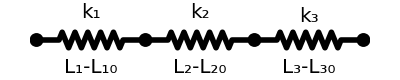

```mathematica
motif= Line[Join[{{-8.5,0},{-5,0}},Table[{-4.5+n,(-1)^n},{n,0,9}],{{5,0},{8.5,0}}]];

spring1 = motif//Translate[#,{-17,0}]&;
spring2 = motif;
spring3 = motif//Translate[#,{17,0}]&;

joints = Point/@{{-25.5,0},{-8.5,0},{8.5,0},{25.5,0}};
annote[{txt_,dirs_,pt_}]:= Text[Style[txt,dirs,FontSize->20],pt]
annotations = annote/@{{"k_1",{},{-17,3.5}},{"L_1-L_10",{},{-17,-3.5}},{"k_2",{},{0,3.5}},{"L_2-L_20",{},{0,-3.5}},{"k_3",{},{17,3}},{"L_3-L_30",{},{17,-3.5}}};
network = {Thickness[0.01],PointSize[0.025],spring1,spring2,spring3,joints,annotations};
Graphics[network]
```

```mathematica
Clear["`*"]
```

(a) Consider a network of three connected springs with different spring constants k_i, different natural lengths L_i0, and different stretched lengths L_i.  When the network of springs is stretched until the total stretched length is twice the total natural length, what will be the stretched length of each individual spring?  In other words, find the L_i in terms of the k_i and the L_i0.

First, the tension in each spring is the same:  k_1(L_1-L_10) = k_2(L_2-L_20) = k_3(L_3-L_30).  This gives us two equations:  k_1 L_1-k_2 L_2 = k_1 L_10-k_2 L_20  and  k_2 L_2-k_3 L_3 = k_2 L_20-k_3 L_30.  But we have three unknown lengths (L_i), and therefore need one more equation -- the total length condition: L_1+ L_2 + L_3 = 2(L_10+ L_20 + L_30).  We could put these equations into a list and use Solve to obtain the answer.  But instead, we will construct the matrix form of these equations and do the linear algebra ourselves to obtain {L_1, L_2, L_3}.

(k_1 | -k_2 | 0
0 | k_2 | -k_3
1 | 1 | 1)(L_1
L_2
L_3)=(k_1 L_10-k_2 L_20
k_2 L_20-k_3 L_30
2 L_10+2 L_20+2 L_30)

```mathematica
M = ({{Subscript[k, 1], -Subscript[k, 2], 0}, {0, Subscript[k, 2], -Subscript[k, 3]}, {1, 1, 1}})
y = ({{Subscript[k, 1] Subscript[L, 10]-Subscript[k, 2] Subscript[L, 20]}, {Subscript[k, 2] Subscript[L, 20]-Subscript[k, 3] Subscript[L, 30]}, {2 Subscript[L, 10]+2 Subscript[L, 20]+2 Subscript[L, 30]}})
Inverse[M].y//Simplify
```

{{k_1,-k_2,0},{0,k_2,-k_3},{1,1,1}}

{k_1 L_10-k_2 L_20,k_2 L_20-k_3 L_30,2 L_10+2 L_20+2 L_30}

{(k_1 (k_2+k_3) L_10+k_2 k_3 (2 L_10+L_20+L_30))/(k_2 k_3+k_1 (k_2+k_3)),(k_2 k_3 L_20+k_1 (k_2 L_20+k_3 (L_10+2 L_20+L_30)))/(k_2 k_3+k_1 (k_2+k_3)),(k_2 k_3 L_30+k_1 (k_3 L_30+k_2 (L_10+L_20+2 L_30)))/(k_2 k_3+k_1 (k_2+k_3))}

(b) Repeat the exercise above for the case of 5 springs.  Evaluate the stretched lengths of each of the springs for the special case where {k1 → 1, k2 → 2, k3 → 3, k4 → 4, k5 → 5}, and each of the unstretched lengths is 137.

```mathematica
Mb = ({{k1, -k2, 0, 0, 0}, {0, k2, -k3, 0, 0}, {0, 0, k3, -k4, 0}, {0, 0, 0, k4, -k4}, {1, 1, 1, 1, 1}});
yb = ({{k1*L10-k2*L20}, {k2*L20-k3*L30}, {k3*L30-k4*L40}, {k4*L40-k5*L50}, {2(L10+L20+L30+L40+L50)}});
LinearSolve[Mb,yb]/.{k1 -> 1, k2 -> 2, k3 -> 3, k4 -> 4, k5 -> 5,L10->137,L20->137,L30->137,L40->137,L50->137}
```

{{11645/28},{15481/56},{6439/28},{23153/112},{26989/112}}

### (#14) Coupled harmonic oscillators (15 min)

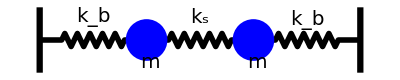

```mathematica
motif= Line[Join[{{-8.5,0},{-5,0}},Table[{-4.5+n,(-1)^n},{n,0,9}],{{5,0},{8.5,0}}]];

spring1 = motif//Translate[#,{-17,0}]&;
spring2 = motif;
spring3 = motif//Translate[#,{17,0}]&;

joints = {Rectangle[{-26,-5},{-25,5}],{Blue,Point[{-8.5,0}],Point[{8.5,0}]},Rectangle[{25,-5},{26,5}]};
annote[{txt_,dirs_,pt_}]:= Text[Style[txt,dirs,FontSize->20],pt]
annotations = annote/@{{"k_b",{},{-17,3.5}},{"m",{},{-8,-3.5}},{"k_s",{},{0,3.5}},{"m",{},{9,-3.5}},{"k_b",{},{17,3}}};
network = {Thickness[0.01],PointSize[0.075],spring1,spring2,spring3,joints,annotations};
Graphics[network]
```

In the mass-spring network above, assume that none of the springs are stretched when the system is in equillibrium.  Consider the time-dependences of the positions of the two masses, x_1(t) and x_2(t), which we define so as to be zero at their equillibrium positions. If the central spring is absent, F = m a = 0 yields m d^2/(d t^2)x_1 = -k_b x_1 for the first spring and m d^2/(d t^2)x_2 = -k_b x_2 for the second.  When the central spring is added, these equations become m d^2/(d t^2)x_1 + k_b x_1 - k_s (x_2-x_1) = 0 and m d^2/dt^2 x_2 + k_b x_2 - k_s (x_1-x_2) = 0, which can also be combined into matrix form as  d^2/(d t^2)x + M·x = 0, where M is a matrix that depends on the spring constants and masses of the network, and x =(x_1
x_2) is a vector containing the two time-dependent positions.

(a) Construct the matrix M associated with the equations above.

```mathematica
Clear["`*"]
```

```mathematica
M = ({{(Subscript[k, b]+Subscript[k, s])/m, -Subscript[k, s]/m}, {-Subscript[k, s]/m, (Subscript[k, b]+Subscript[k, s])/m}})
```

{{(k_b+k_s)/m,-k_s/m},{-k_s/m,(k_b+k_s)/m}}

(b) Evaluate the cell below to see how the differential equations of motion can be constructed using M and solved to obtain the time-dependent positions of the two masses.

```mathematica
unknowns ={x1[t],x2[t]};
equations = (#==0&)/@ (D[unknowns,t,t]+M.unknowns)
initialconditions = {x1[0]==x10,x1'[0]==v10,x2[0]==x20,x2'[0]==v20}
positions = unknowns/.DSolve[{equations,initialconditions},unknowns,t][[1]]
```

{((k_b+k_s) x1[t])/m-(k_s x2[t])/m+x1''[t]==0,-(k_s x1[t])/m+((k_b+k_s) x2[t])/m+x2''[t]==0}

{x1[0]==x10,x1'[0]==v10,x2[0]==x20,x2'[0]==v20}

{1/(4 √k_b √(-m (k_b+2 k_s)))ⅇ^(-(ⅈ t √k_b)/(√m)-(t √(-m (k_b+2 k_s)))/m) (-ⅇ^((ⅈ t √k_b)/(√m)) m v10 √k_b+ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) m v10 √k_b+ⅇ^((ⅈ t √k_b)/(√m)) m v20 √k_b-ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) m v20 √k_b+ⅈ ⅇ^((t √(-m (k_b+2 k_s)))/m) √m v10 √(-m (k_b+2 k_s))-ⅈ ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) √m v10 √(-m (k_b+2 k_s))+ⅈ ⅇ^((t √(-m (k_b+2 k_s)))/m) √m v20 √(-m (k_b+2 k_s))-ⅈ ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) √m v20 √(-m (k_b+2 k_s))+ⅇ^((ⅈ t √k_b)/(√m)) x10 √k_b √(-m (k_b+2 k_s))+ⅇ^((t √(-m (k_b+2 k_s)))/m) x10 √k_b √(-m (k_b+2 k_s))+ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) x10 √k_b √(-m (k_b+2 k_s))+ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) x10 √k_b √(-m (k_b+2 k_s))-ⅇ^((ⅈ t √k_b)/(√m)) x20 √k_b √(-m (k_b+2 k_s))+ⅇ^((t √(-m (k_b+2 k_s)))/m) x20 √k_b √(-m (k_b+2 k_s))+ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) x20 √k_b √(-m (k_b+2 k_s))-ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) x20 √k_b √(-m (k_b+2 k_s))),1/(4 √k_b √(-m (k_b+2 k_s)))ⅇ^(-(ⅈ t √k_b)/(√m)-(t √(-m (k_b+2 k_s)))/m) (ⅇ^((ⅈ t √k_b)/(√m)) m v10 √k_b-ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) m v10 √k_b-ⅇ^((ⅈ t √k_b)/(√m)) m v20 √k_b+ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) m v20 √k_b+ⅈ ⅇ^((t √(-m (k_b+2 k_s)))/m) √m v10 √(-m (k_b+2 k_s))-ⅈ ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) √m v10 √(-m (k_b+2 k_s))+ⅈ ⅇ^((t √(-m (k_b+2 k_s)))/m) √m v20 √(-m (k_b+2 k_s))-ⅈ ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) √m v20 √(-m (k_b+2 k_s))-ⅇ^((ⅈ t √k_b)/(√m)) x10 √k_b √(-m (k_b+2 k_s))+ⅇ^((t √(-m (k_b+2 k_s)))/m) x10 √k_b √(-m (k_b+2 k_s))+ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) x10 √k_b √(-m (k_b+2 k_s))-ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) x10 √k_b √(-m (k_b+2 k_s))+ⅇ^((ⅈ t √k_b)/(√m)) x20 √k_b √(-m (k_b+2 k_s))+ⅇ^((t √(-m (k_b+2 k_s)))/m) x20 √k_b √(-m (k_b+2 k_s))+ⅇ^((2 ⅈ t √k_b)/(√m)+(t √(-m (k_b+2 k_s)))/m) x20 √k_b √(-m (k_b+2 k_s))+ⅇ^((ⅈ t √k_b)/(√m)+(2 t √(-m (k_b+2 k_s)))/m) x20 √k_b √(-m (k_b+2 k_s)))}

(c)  Evaluate the time-dependent positions of the two masses for the special case where the central spring is much weaker than the springs on either side (i.e. k_b → 1 and k_s → 0.1), and m → 1, and all of the initial velocities and positions are zero except for x_10 → 1.  Then plot these two positions over the range {t, 0, 100} on the same graph using PlotStyle → {{Thick, Red}, {Thick, Blue}}.  Explain this behavior (called "mode coupling") to your TA.  Hint: If the plot looks a little choppy, try eliminating the imaginary contributions to the time dependence that arise due to computer-roundoff error.

{(0.-0.228218 ⅈ) ⅇ^((0.-2.09545 ⅈ) t) ((0.+0. ⅈ)+(0.+1.09545 ⅈ) ⅇ^(ⅈ t)+(0.+1.09545 ⅈ) ⅇ^((0.+1.09545 ⅈ) t)+(0.+1.09545 ⅈ) ⅇ^((0.+3.09545 ⅈ) t)+(0.+1.09545 ⅈ) ⅇ^((0.+3.19089 ⅈ) t)),(0.-0.228218 ⅈ) ⅇ^((0.-2.09545 ⅈ) t) ((0.+0. ⅈ)-(0.+1.09545 ⅈ) ⅇ^(ⅈ t)+(0.+1.09545 ⅈ) ⅇ^((0.+1.09545 ⅈ) t)+(0.+1.09545 ⅈ) ⅇ^((0.+3.09545 ⅈ) t)-(0.+1.09545 ⅈ) ⅇ^((0.+3.19089 ⅈ) t))}

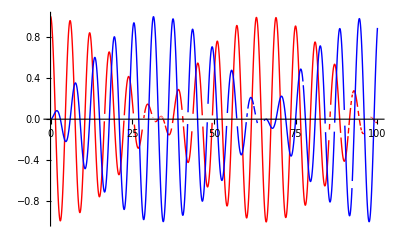

```mathematica
plotpositions = positions/.{Subscript[k, b]->1,Subscript[k, s]->0.1,m->1,x10->1,v10->0,x20->0,v20->0}
Plot[{plotpositions},{t,0,100},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

## On Your Own (45 min)

### (#15) Principal Axes (15 min)

The moment of inertia of a rectangular object with density ρ(x,y,z) is given by the following I_ij=∫_-a^a ∫_-b^b ∫_-c^c r_i r_j ρ(x,y,z)ⅆzⅆyⅆx.  In this expression, r_1=x, r_2=y, and r_3=z.  If ρ(x,y,z)=cos((z-0.1)/π) exp(-((x-0.5)^2+(y+0.2)^2)/0.7), what are the principal axes of the system?  What is the moment of inertia about each of these axes if a=1, b=1.5, c=2?

```mathematica
r[1]=x;
r[2]=y;
r[3]=z;
Table[r[i]*r[j],{i,1,3},{j,1,3}];
solutions = Table[Integrate[r[i]*r[j]*Cos[(z-0.1)/π]*Exp[-((x-0.5)^2+(y+0.2)^2)/0.7],{z,-2,2},{y,-1.5,1.5},{x,-1,1}],{i,1,3},{j,1,3}]
```

{{1.81587+0. ⅈ,-0.356666+0. ⅈ,0.0271664+0. ⅈ},{-0.356666+0. ⅈ,2.23932+0. ⅈ,-0.0162846+0. ⅈ},{0.0271664+0. ⅈ,-0.0162846+0. ⅈ,8.08562+0. ⅈ}}

```mathematica
solutions//MatrixForm
```

(1.81587+0. ⅈ | -0.356666+0. ⅈ | 0.0271664+0. ⅈ
-0.356666+0. ⅈ | 2.23932+0. ⅈ | -0.0162846+0. ⅈ
0.0271664+0. ⅈ | -0.0162846+0. ⅈ | 8.08562+0. ⅈ)

```mathematica
c = Transpose[Eigenvectors[solutions]];
d = Inverse[c].solutions.c;
Diagonal[d]//MatrixForm
```

(8.08579+0. ⅈ
2.44224+0. ⅈ
1.61279+0. ⅈ)

### (#16) Binary Star (20 min)

Two stars with masses m_1 and m_2 are attracted to each other by the gravitational force.  Using units where m is measured in solar masses and r is in units of about 10^10 meters, and appropriate units of time, G will be 1.  In these units, the first star m1=1 starts at a position (15,2.5).  The second star starts at a position (-5,0).  The first star has an initial veloicty of (-0.2,0.12).  The second has an initial velocity of (0.1,-0.15).  If d_12 is the distance between the two stars, d_12=√((x_2(t)-x_1(t))^2+(y_2(t)-y_1(t))^2), Newton’s Law of gravity says the acceleration of the first star will be a_x=x_1''(t)=(m_2 (x_2(t)-x_1(t)))/d_12^3.  The equations for the other components of each star are similar.  Draw an animation showing the position of the two stars for t=0,1000.  You’ll probably need to use NDSolve to solve the system of equations and initial conditions you generate.

```mathematica
Clear["`*"]
```

```mathematica
m1=1;
m2=1;
p10 = {x10,y10}={15,2.5};
v10 = {-0.2,0.12};
p20 ={x20,y20}= {-5,0};
v20 = {0.1,-0.15};
d12 = √((x2[t]-x1[t])^2+(y2[t]-y1[t])^2);
```

```mathematica
equationMatrix=({{(m2 (-x1[t]+x2[t]))/d12^3, (m1 (-x2[t]+x1[t]))/d12^3}, {(m2 (-y1[t]+y2[t]))/d12^3, (m1 (-y2[t]+y1[t]))/d12^3}});
```

```mathematica
answers = NDSolve[{
x1''[t]==equationMatrix[[1,1]],
x2''[t]==equationMatrix[[1,2]],
y1''[t]==equationMatrix[[2,1]],
y2''[t]==equationMatrix[[2,2]],
x1[0]==x10,
x2[0]==x20,
x1'[0]==v10[[1]],
x2'[0]==v20[[1]],
y1[0]==y10,
y2[0]==y20,
y1'[0]==v10[[2]],
y2'[0]==v20[[2]]
},
{x1,x2,y1,y2},
{t,0,2500}
][[1]]
```

{x1→InterpolatingFunction[{{0.,2500.}},<>],x2→InterpolatingFunction[{{0.,2500.}},<>],y1→InterpolatingFunction[{{0.,2500.}},<>],y2→InterpolatingFunction[{{0.,2500.}},<>]}

```mathematica
{x1f,x2f,y1f,y2f}={x1,x2,y1,y2}/.answers
```

{InterpolatingFunction[{{0.,2500.}},<>],InterpolatingFunction[{{0.,2500.}},<>],InterpolatingFunction[{{0.,2500.}},<>],InterpolatingFunction[{{0.,2500.}},<>]}

```mathematica
Animate[Graphics[{Red,Disk[{x1f[t],y1f[t]},2],Blue,Disk[{x2f[t],y2f[t]},2]},PlotRange->{{-150,150},{-150,150}}],{t,1,2500}]
```

### (#17) Stationary States (10 min)

A certain atom can be nicely modelled as having three states with energies 1.0, 1.7, and 2.5.  (Atoms, of course, have an infinite number of possible states, but often only a few are important in problems like this one.)   These means that the atomic states can be represented as vectors {ψ_1, ψ_2, ψ_3} and the Hamiltonian as a diagonal matrix H={{1.0,0,0},{0,1.7,0},{0,0,2.5}}.  If a laser is shined on the atom, it couples the levels so that the new Hamiltonian is

```mathematica
H1 = {{1.0,0,0},{0,1.7,0},{0,0,2.5}};
H={{1.0, 0.1I, 0},{-0.1I, 1.7, 0.2I},{0, -0.2I, 2.5}};
MatrixForm/@{H1,H}
```

{(1. | 0 | 0
0 | 1.7 | 0
0 | 0 | 2.5),(1. | 0.+0.1 ⅈ | 0
0.-0.1 ⅈ | 1.7 | 0.+0.2 ⅈ
0 | 0.-0.2 ⅈ | 2.5)}

What the the energies of the new system and the new eigenstates corresponding to these energies?

```mathematica
Eigensystem[H]//MatrixForm
eigval=Eigenvalues[H];
eigvec=Eigenvectors[H];
ans = {eigval,eigvec}//MatrixForm
```

(2.54756 | 1.66698 | 0.985468
{-0.0149467,0.+0.231309 ⅈ,0.972765} | {0.144263,0.-0.962196 ⅈ,0.231013} | {0.989427,0.+0.143787 ⅈ,-0.0189876})

(2.54756 | 1.66698 | 0.985468
{-0.0149467,0.+0.231309 ⅈ,0.972765} | {0.144263,0.-0.962196 ⅈ,0.231013} | {0.989427,0.+0.143787 ⅈ,-0.0189876})